```mathematica
Clear["Global`*"]
```

```mathematica
nMat=1.444;
k0=2Pi/λ;
rMax=25;
rCore=8.2/2;
percn=0.0036;
c=3*10^8/1000/10^12;
η0=120*π;
nMax=nMat*(1+percn);
β=neff*k0;
```

```mathematica
u=Sqrt[(k0^2*(nMat(1+percn))^2)-β^2];
w=Sqrt[β^2-(k0*nMat)^2];
V=Sqrt[(k0*rCore)^2*((nMat*(1+percn))^2-nMat^2)];
n[r_]=(percn*HeavisideTheta[rCore-r]+1)*nMat;
ez[r_,ϕ_]=
Piecewise[{{η0*A*BesselJ[l,u*r]/BesselJ[l,u*rCore]*Cos[l*ϕ],r<=rCore},{η0*A*BesselK[l,w*r]/BesselK[l,w*rCore]*Cos[l*ϕ],r>rCore}}];
hz[r_,ϕ_]=
Piecewise[{{B*BesselJ[l,u*r]/BesselJ[l,u*rCore](-Sin[l*ϕ]),r<=rCore},{B*BesselK[l,w*r]/BesselK[l,w*rCore]*(-Sin[l*ϕ]),r>rCore}}];
er[r_,ϕ_]=-I/(k0^2*(n[r])^2-β^2)*(β*D[ez[r,ϕ],r]+η0*k0/r*D[hz[r,ϕ],ϕ]);
eϕ[r_,ϕ_]=-I/(k0^2*(n[r])^2-β^2)*(β/r*D[ez[r,ϕ],ϕ]-η0*k0*D[hz[r,ϕ],r]);
hr[r_,ϕ_]=-I/(k0^2*(n[r])^2-β^2)*(-1/η0*k0*(n[r])^2/r*D[ez[r,ϕ],ϕ]+β*D[hz[r,ϕ],r]);
hϕ[r_,ϕ_]=-I/(k0^2*(n[r])^2-β^2)*(1/η0*k0*(n[r])^2*D[ez[r,ϕ],r]+β/r*D[hz[r,ϕ],ϕ]);
```

```mathematica
(*поиск neff*)
```

```mathematica
harEq=(D[BesselJ[l,x],x]/(x*BesselJ[l,x])+D[BesselK[l,y],y]/(y*BesselK[l,y]))*(D[BesselJ[l,x],x]/(x*BesselJ[l,x])+(nMat/nMax)^2*D[BesselK[l,y],y]/(y*BesselK[l,y]))-(l*β/k0/nMax)^2*(V/(u*rCore*w*rCore))^4/.{x->u*rCore,y->w*rCore};
```

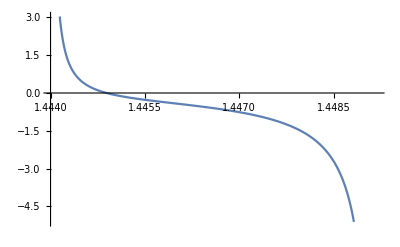

```mathematica
Plot[harEq/.{λ->1.06,l->2},{neff,nMat,nMax}/.λ->1.06,AxesOrigin->{nMat,0}]
```

```mathematica
solneff=FindRoot[harEq/.{λ->1.06,l->2},{neff,1.445}]
```

{neff→1.44489}

```mathematica
(*поиск отношения A к B*)
solB=Solve[-A*l*β/(u*rCore)^2+B*k0*D[BesselJ[l,x],x]/(x*BesselJ[l,x])==A*l*β/(w*rCore)^2-B*k0*D[BesselK[l,y],y]/(y*BesselK[l,y])/.{x->u*rCore,y->w*rCore}/.solneff/.{λ->1.06,l->2},B]
```

{{B→-1.44377 A}}

```mathematica
(*Вектор Пойнтинга*)
```

```mathematica
sr[r_,ϕ_]=Det[({{eϕ[r,ϕ], ez[r,ϕ]}, {(hϕ[r,ϕ])*, (hz[r,ϕ])*}})];
sϕ[r_,ϕ_]=-Det[({{er[r,ϕ], ez[r,ϕ]}, {(hr[r,ϕ])*, (hz[r,ϕ])*}})];sz[r_,ϕ_]=Det[({{er[r,ϕ], eϕ[r,ϕ]}, {(hr[r,ϕ])*, (hϕ[r,ϕ])*}})];
```

```mathematica
sr[10,0]/.solneff/.{λ->1.06,l->2}/.solB/.A->1
```

{0.-39.5663 ⅈ}

```mathematica
int[r_,ϕ_]=ComplexExpand[Abs[sr[r,ϕ]^2+sϕ[r,ϕ]^2+sz[r,ϕ]^2]]/.solneff/.{λ->1.06,l->2}/.solB/.A->1;
```

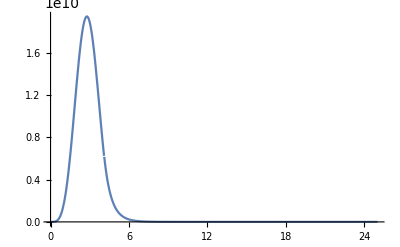

```mathematica
Plot[int[r,0],{r,0,rMax},PlotRange->All]
```

```mathematica
ParametricPlot3D[{r*Cos[ϕ],r*Sin[ϕ],int[r,ϕ][[1]]},{ϕ,0,2*π},{r,0,rMax},BoxRatios->{1,1,1},PlotRange->All]
```

-Graphics3D-

```mathematica
ex[x_,y_]:=Simplify[Abs[(er[r,ϕ]*Cos[ϕ]-eϕ[r,ϕ]*Sin[ϕ])]/.solneff/.{λ->1.06,l->2}/.solB[[1]]/.A->1/.{r->Sqrt[x^2+y^2],ϕ->ArcTan[x/y]},Assumptions->√(x^2+y^2)<rCore];
ey[x_,y_]=Simplify[Abs[(er[r,ϕ]*Sin[ϕ]+eϕ[r,ϕ]*Cos[ϕ])]/.solneff/.{λ->1.06,l->2}/.solB/.A->1/.{r->Sqrt[x^2+y^2],ϕ->ArcTan[x/y]},Assumptions->√(x^2+y^2)<rCore];
```

```mathematica
ex[x,y];
```

Simplify::fas: Warning: one or more assumptions evaluated to False.

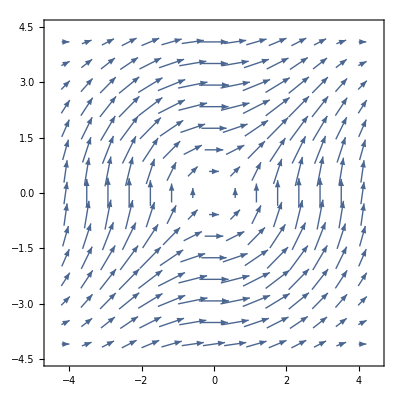

```mathematica
VectorPlot[{ex[x,y],ey[x,y]},{x,-rCore,rCore},{y,-rCore,rCore}]
```

```mathematica
(*Волокно SMF28*)
```

```mathematica
(*l=0*)
votsTETM=Table[BesselJZero[0,m],{m,10}];
(*l≥1 EH моды (знак плюс в решении квадратного уравниения отснсительно J'/J*)
```

```mathematica
votsEH=Table[Table[BesselJZero[l,m],{m,10}],{l,10}];
```

```mathematica
(*l=1 HE моды (знак минус в решении квадратного уравниения отснсительно J'/J*)
```

```mathematica
votsHE[1]=Table[BesselJZero[1,m],{m,10}];
```

```mathematica
(*l≥2 HE моды (знак минус в решении квадратного уравниения отснсительно J'/J*)
```

```mathematica
FindRoot[BesselJ[l-2,v]+(nMax^2-nMat^2)/(nMax^2+nMat^2)*BesselJ[l,v]==0/.l->3,{v,1}]
```

{v→1.23879×10^-20}